```mathematica
(* See if the plots of the dispersion equation actually make sense *)
(* only consider the TE mode for now *)
(* in C++ calculation disp eqn is discontinuous across search space *)
(* this should not be the case *)
(* R. Sheehan 18 - 12 - 2020 *)
```

```mathematica
nc = 3.38; (* core RI *)
nr = 3.17; (* rib RI *)
ns=2.0; (* substrate RI *)
ncl=1.0; (* cladding RI *)
λ=1.55;(* wavelength in units of um *)
W=1.5;(* core width units of um *)
Dr=1.5;(* rib width units of um *)
k=(2π)/λ; (* wavenumber *)
(*lower=k Max[ns, ncl];*)(* This is required to ensure that search space will only occur over real valued functions *)
(*upper = k nr;*)
lower=k Max[ns, ncl,nr];
upper = k nc;
kncsqr = (k nc)^2; 
knrsqr = (k nr)^2; 
knclsqr = (k ncl)^2; 
knsqr = (k ns)^2;
```

```mathematica
lower
```

12.8501

```mathematica
upper
```

13.7014

```mathematica
p[x_]:=√(x^2-knsqr);
q[x_]:=√(x^2-knclsqr);
h[x_]:=√(kncsqr-x^2);
(*r[x_]:=√(knrsqr-x^2);*)
r[x_]:=√(x^2-knrsqr); 
(*phase[x_,m_]:=ArcTan[q[x]/r[x]]-Dr r[x]-m π; *)
phase[x_]:=-ArcTanh[q[x]/r[x]]-Dr r[x];
F1[x_]:=p[x]/h[x];
F2[x_]:=r[x]/h[x];
F3[x_]:=Tan[phase[x]];
```

```mathematica
Print["h[lower]:",h[lower],", h[upper]: ",h[upper]]
Print["r[lower]:",r[lower],", r[upper]: ",r[upper]]
Print["p[lower]:",p[lower],", p[upper]: ",p[upper]]
Print["q[lower]:",q[lower],", q[upper]: ",q[upper]]
Print["ψ[lower]:",phase[lower],", ψ[upper]: ",phase[upper]]
(*Print["Tan[ψ[lower]]:",Tan[phase[lower,0]],", Tan[ψ[upper]]: ",Tan[phase[upper,0]]]
Print["r[lower]/h[lower]:",r[lower]/h[lower],", r[upper]/h[upper]: ",r[upper]/h[upper]]
Print["(r[lower]/h[lower])Tan[ψ[lower]]:",r[lower]/h[lower] Tan[phase[lower,0]],", (r[upper]/h[upper])Tan[ψ(upper)]: ",r[upper]/h[upper] Tan[phase[upper,0]]]*)
```

h[lower]:4.75421, h[upper]: 0.

r[lower]:0., r[upper]: 4.75421

p[lower]:9.9698, p[upper]: 11.0453

q[lower]:12.194, q[upper]: 13.088

Power::infy: Infinite expression 1/0. encountered.

ψ[lower]:Indeterminate, ψ[upper]: -7.51194+1.5708 ⅈ

## Hacking Jan 7th 2021

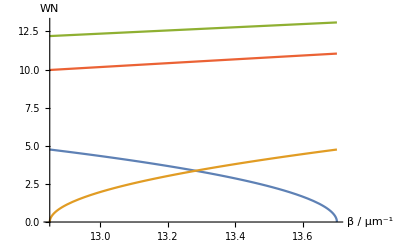

```mathematica
Plot[{h[x],r[x],q[x],p[x]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","WN"}]
```

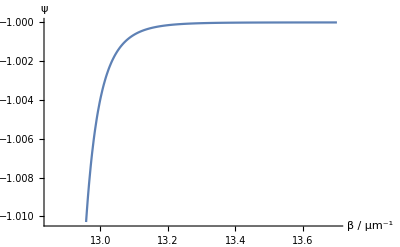

```mathematica
Plot[{Tanh[phase[x]]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ψ"}]
```

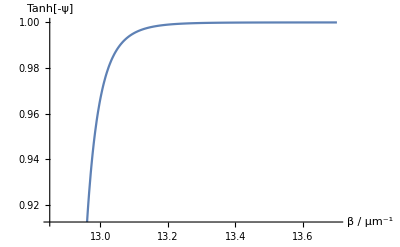

```mathematica
Plot[{(1-q[x]/r[x] ⅇ^(-2 Dr r[x]))/(1+q[x]/r[x] ⅇ^(-2 Dr r[x]))},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","Tanh[-ψ]"}]
```

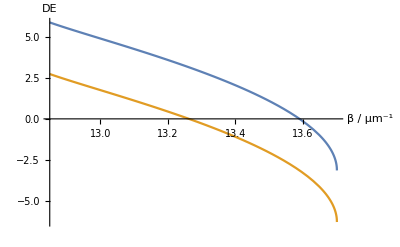

```mathematica
m=1;
Plot[{W h[x]-ArcTan[p[x]/h[x]]-ArcTan[r[x]/h[x]((1-(r[x]-q[x])/(r[x]+q[x])ⅇ^(-2 Dr r[x]))/(1+(r[x]-q[x])/(r[x]+q[x])ⅇ^(-2 Dr r[x])))]-(m-1)π,W h[x]-ArcTan[p[x]/h[x]]-ArcTan[r[x]/h[x]((1-(r[x]-q[x])/(r[x]+q[x])ⅇ^(-2 Dr r[x]))/(1+(r[x]-q[x])/(r[x]+q[x])ⅇ^(-2 Dr r[x])))]-π},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","DE"}]
```

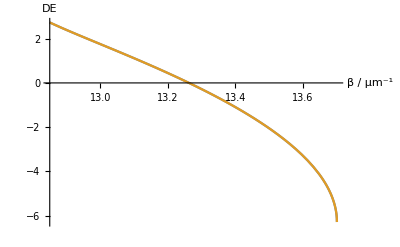

```mathematica
m=2;
Plot[{W h[x]-ArcTan[p[x]/h[x]]-ArcTan[r[x]/h[x] Tanh[-phase[x]]]-(m-1)π,W h[x]-ArcTan[p[x]/h[x]]-ArcTan[r[x]/h[x]((1-(r[x]-q[x])/(r[x]+q[x])ⅇ^(-2 Dr r[x]))/(1+(r[x]-q[x])/(r[x]+q[x])ⅇ^(-2 Dr r[x])))]-(m-1)π},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","DE"}]
```

```mathematica
m=2;
FindRoot[W h[x]-ArcTan[p[x]/h[x]]-ArcTan[r[x]/h[x] Tanh[-phase[x]]]-(m-1)π==0,{x,(upper+lower)/2}]
```

General::munfl: ArcTan[0.984148-6.34941×10^-21 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

{x→13.2629+0. ⅈ}

```mathematica
m=1;
FindRoot[W h[x]-ArcTan[p[x]/h[x]]-ArcTan[r[x]/h[x]((1-(r[x]-q[x])/(r[x]+q[x])ⅇ^(-2 Dr r[x]))/(1+(r[x]-q[x])/(r[x]+q[x])ⅇ^(-2 Dr r[x])))]-(m-1)π==0,{x,(upper+lower)/2}]
```

{x→13.5906}

```mathematica
Abs[N[ArcTanh[4]/(π/2)]]
```

1.01313

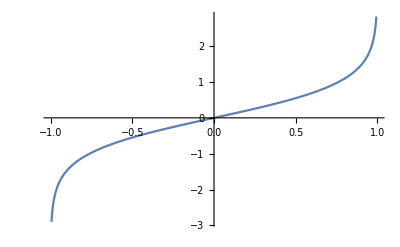

```mathematica
Plot[ArcTanh[x],{x,-1,1}]
```

## Hacking Jan 6th 2021

```mathematica
(* Discontinuities arise whenever Subscript[ψ, a] = Tan^-1(q/r)-D r = m π / 2, m odd integer *)
(* Tan[Subscript[ψ, a]] -> ∞ when Subscript[ψ, a] -> m π / 2, m odd integer *)
```

```mathematica
Dr=1.5;
```

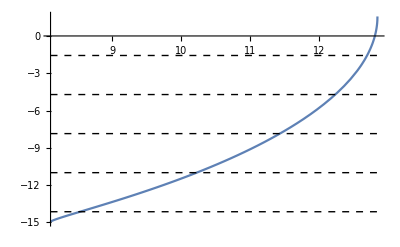

```mathematica
Plot[ArcTan[q[x]/r[x]]-Dr r[x],{x,lower, upper},
Epilog->{
{Thick, Dashed, Line[{{lower,-π/2},{upper,-π/2}}]},
{Thick, Dashed, Line[{{lower,-3 π/2},{upper,-3 π/2}}]},
{Thick, Dashed, Line[{{lower,-5 π/2},{upper,-5 π/2}}]},
{Thick, Dashed, Line[{{lower,-7 π/2},{upper,-7 π/2}}]},
{Thick, Dashed, Line[{{lower,-9 π/2},{upper,-9 π/2}}]}
}]
```

```mathematica
FindRoot[ArcTan[q[x]/r[x]]-Dr r[x]+9 π/2==0,{x,12}]
```

{x→8.53577}

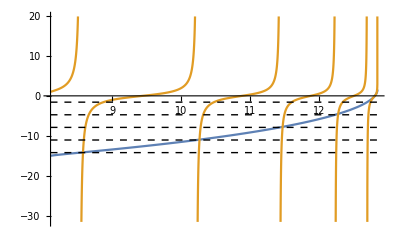

```mathematica
Plot[{ArcTan[q[x]/r[x]]-Dr r[x],Tan[ArcTan[q[x]/r[x]]-Dr r[x]]},{x,lower, upper},
Epilog->{
{Thick, Dashed, Line[{{lower,-π/2},{upper,-π/2}}]},
{Thick, Dashed, Line[{{lower,-3 π/2},{upper,-3 π/2}}]},
{Thick, Dashed, Line[{{lower,-5 π/2},{upper,-5 π/2}}]},
{Thick, Dashed, Line[{{lower,-7 π/2},{upper,-7 π/2}}]},
{Thick, Dashed, Line[{{lower,-9 π/2},{upper,-9 π/2}}]}
}]
```

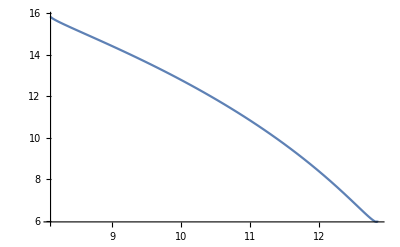

```mathematica
Plot[W h[x]-ArcTan[p[x]/h[x]]-ArcTan[r[x]/h[x]],{x,lower,upper}]
```

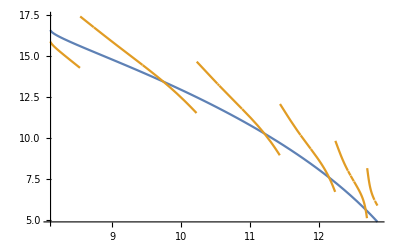

```mathematica
Plot[{W h[x]-ArcTan[p[x]/h[x]]-ArcTan[q[x]/h[x]],W h[x]-ArcTan[p[x]/h[x]]-ArcTan[r[x]/h[x](q[x]/r[x]-Tan[Dr r[x]])/(1+q[x]/r[x] Tan[Dr r[x]])]},{x,lower,upper}]
```

## Hacking Dec 18th 2020

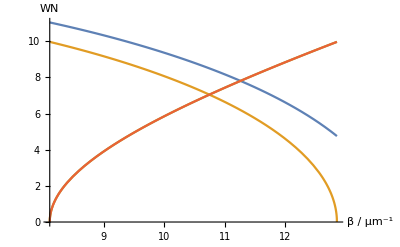

```mathematica
Plot[{h[x],r[x],q[x],p[x]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","WN"}]
```

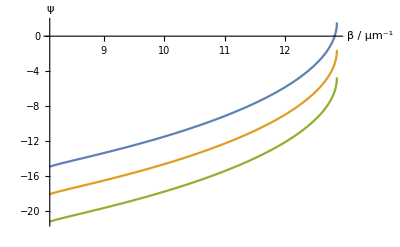

```mathematica
Plot[{phase[x,0],phase[x,1],phase[x,2]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ψ"}]
```

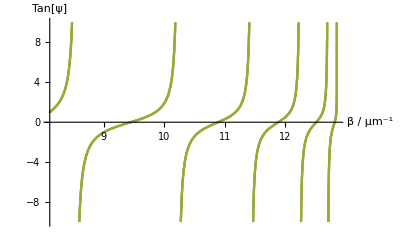

```mathematica
Plot[{Tan[phase[x,0]],Tan[phase[x,1]],Tan[phase[x,2]]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","Tan[ψ]"},PlotRange->{{lower, upper},{-10,10}}]
```

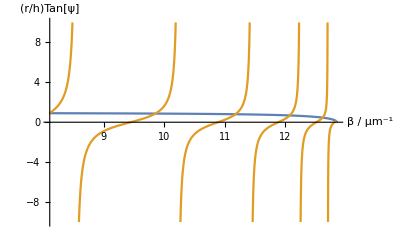

```mathematica
Plot[{(r[x]/h[x]),(r[x]/h[x])Tan[phase[x,0]]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","(r/h)Tan[ψ]"},PlotRange->{{lower, upper},{-10,10}}]
```

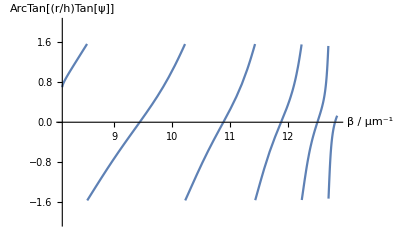

```mathematica
Plot[{ArcTan[(r[x]/h[x])Tan[phase[x,0]]]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(r/h)Tan[ψ]]"},PlotRange->{{lower, upper},{-2,2}}]
```

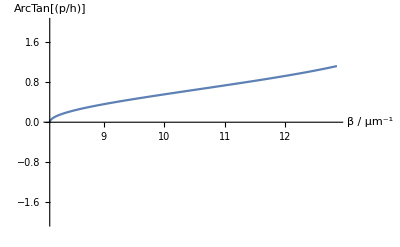

```mathematica
Plot[{ArcTan[(p[x]/h[x])]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"},PlotRange->{{lower, upper},{-2,2}}]
```

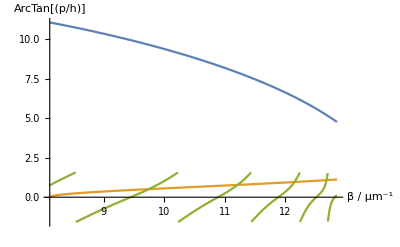

```mathematica
Plot[{W h[x],ArcTan[(p[x]/h[x])],ArcTan[(r[x]/h[x])Tan[phase[x,0]]]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"}]
```

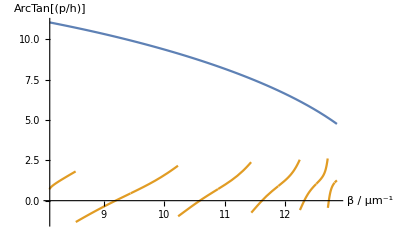

```mathematica
Plot[{W h[x],ArcTan[(p[x]/h[x])]+ArcTan[(r[x]/h[x])Tan[phase[x,0]]]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"}]
```

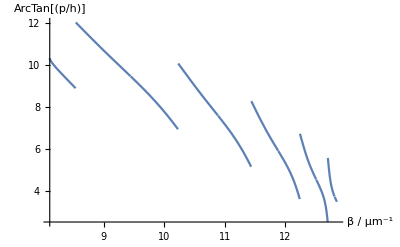

```mathematica
Plot[{W h[x]-ArcTan[(p[x]/h[x])]-ArcTan[(r[x]/h[x])Tan[phase[x,0]]]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"}]
```

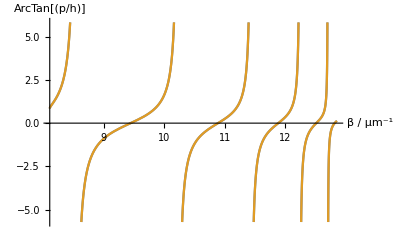

```mathematica
Plot[{(r[x]/h[x])Tan[phase[x,0]],F2[x] F3[x]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"}]
```

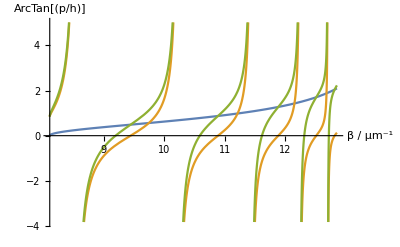

```mathematica
Plot[{F1[x],F2[x] F3[x],F1[x]+F2[x] F3[x]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"}]
```

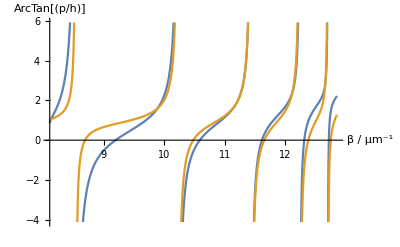

```mathematica
Plot[{F1[x]+F2[x] F3[x],1+F1[x]F2[x] F3[x]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"}]
```

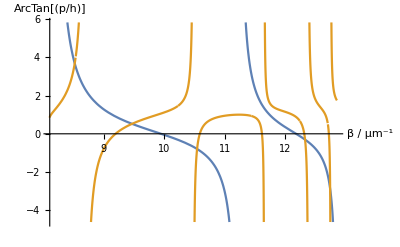

```mathematica
Plot[{Tan[W h[x]],(F1[x]+F2[x] F3[x])/(1+F1[x]F2[x]F3[x])},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","ArcTan[(p/h)]"}]
```

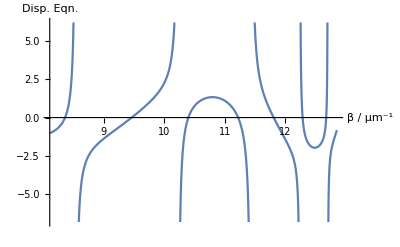

```mathematica
Plot[{Sin[W h[x]](1-F1[x]F2[x]F3[x])-Cos[W h[x]](F1[x]+F2[x]F3[x])},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","Disp. Eqn."}]
```

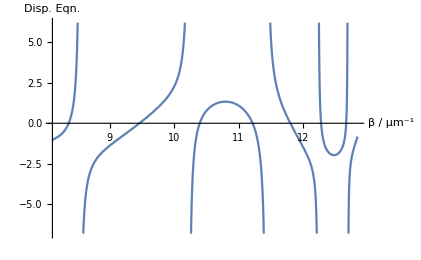

```mathematica
Plot[{Sin[W h[x]]-F1[x]Cos[W h[x]]-(Cos[W h[x]]+F1[x]Sin[W h[x]])F2[x]F3[x]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","Disp. Eqn."}]
```

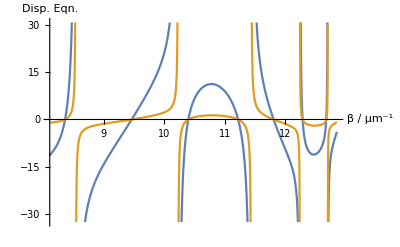

```mathematica
Plot[{h[x] Sin[W h[x]]-p[x]Cos[W h[x]]-(Cos[W h[x]]+p[x]/h[x] Sin[W h[x]])r[x]F3[x],Sin[W h[x]]-F1[x]Cos[W h[x]]-(Cos[W h[x]]+F1[x]Sin[W h[x]])F2[x]F3[x]},{x,lower, upper},AxesStyle->Thick,LabelStyle->Bold,AxesLabel->{"β / μm^-1","Disp. Eqn."}]
```

```mathematica
FindRoot[Sin[W h[x]]-F1[x]Cos[W h[x]]-(Cos[W h[x]]+F1[x]Sin[W h[x]])F2[x]F3[x]==0,{x,9}]
```

{x→9.46052}

```mathematica
FindRoot[Sin[W h[x]]-F1[x]Cos[W h[x]]-(Cos[W h[x]]+F1[x]Sin[W h[x]])F2[x]F3[x]==0,{x,10.5}]
```

{x→10.3968}

```mathematica
FindRoot[Sin[W h[x]]-F1[x]Cos[W h[x]]-(Cos[W h[x]]+F1[x]Sin[W h[x]])F2[x]F3[x]==0,{x,11.2}]
```

{x→11.2187}

```mathematica
FindRoot[Sin[W h[x]]-F1[x]Cos[W h[x]]-(Cos[W h[x]]+F1[x]Sin[W h[x]])F2[x]F3[x]==0,{x,11.9}]
```

{x→11.805}

```mathematica
FindRoot[ h[x]Sin[W h[x]]-p[x]Cos[W h[x]]-(Cos[W h[x]]+p[x]/h[x] Sin[W h[x]])r[x]F3[x]==0,{x,10.5}]
```

{x→10.3968}